```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.50 (21 Nov 2014)) loaded Sun 21 Aug 2016 22:24:12
using xCellerator 0.95 and XSSA 1.3.0
GPL License Terms Apply

```mathematica
<<xlr8r.m
```

xCellerator 0.95 (28-Feb-2014) loaded Sun 21 Aug 2016 22:24:13
using Mathematica 8.0 for Microsoft Windows (64-bit) (October 6, 2011) (Version 8., Release 4)

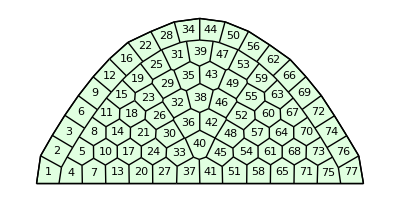

```mathematica
(*qq = Tissue2DTissue[TemplateParabolic[30,7,0.01]];*)
qq = TemplateParabolic[30,7,0.01];
ShowTissue[qq, "CellNumbers" -> True]
```

{1,2,3,4,6,7,9,12,13,16,20,22,27,28,34,37,41,44,50,51,56,58,62,65,66,69,71,72,74,75,76,77}

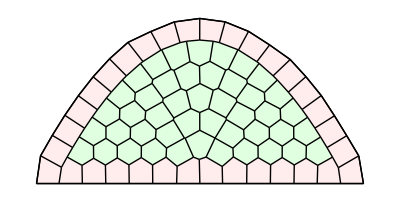

```mathematica
L1Layer = CellsOnBoundary[qq]
ShowTissueCells[qq,L1Layer]
```

```mathematica
NeighborQ[qq,{6,8}]
```

True

```mathematica
L1[i] -> If[MemberQ[L1Layer,i],1,0];
```

```mathematica
L1delta[i_] := If[MemberQ[L1Layer,i],1,0];
```

```mathematica
L2delta[j_] := (numN = 0; Do[ numN = numN + If[ NeighborQ[qq,{i,j}] && !MemberQ[L1Layer,j], 1, 0], {i,L1Layer}]; If[numN>0,1,0])
```

```mathematica
L2Layer = {};
Do[ If[ L2delta[jj]==1, L2Layer = Append[L2Layer,jj],0], {jj,1,NTissueCells[qq]}];
```

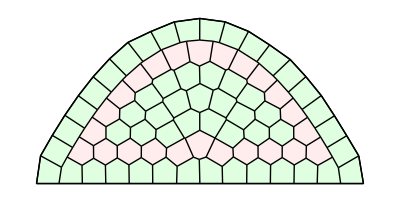

```mathematica
ShowTissueCells[qq,L2Layer]
```

```mathematica
L2[i] -> If[L2delta[i]==1,1,0]
```

L2[i]→0

```mathematica
Wnet = { 
{∅-> U, k1*Tip[t]}, 
{U -> ∅, k2},
{U -> U, Diffusion[DU]},
{∅ -> V, k3 * L1[t]},
{V -> ∅, k4},
{V -> V, Diffusion[DV]},
{∅ ⇄ Z, k7, k8*U[t]},
{X ↦ V, GRN[vV,Twv,1,hV]},
{ {U,V,W} ↦ W, GRN[vW, {TUW,TVW,TWW}, 1, hW] },
{W -> ∅, k6*Z[t] + k9*L2[t]},
{W ↦ X, GRN[vX,TWX,1,hX]},
{X -> ∅, k5},
{X -> X, Diffusion[DX]},
{cell -> cell, Grow[GrowthRate[mu,fmu]],Pressure[P,fP],Spring[k,fk]},
{cell -> cell + cell, Errera[cell, mu, sigmaVar]}
}
```

```mathematica
qq2 = DeleteCell[qq,5];
```

```mathematica
ShowTissue[qq2,"CellNumbers" -> True];
```

```mathematica
L2Layer = CellsOnBoundary[qq2]; 
ShowTissueCells[qq,L2Layer];
```

{Tissue[{{-30.458,1.20462},«152»,{«1»}},{«1»},{«1»}],CellsOnBoundary[DeleteCell[Tissue[«1»],5]]}15

Error: Expecting ShowTissueCells[tissue, {i1,i2,...}] or 
ShowTissueCells[tissue, {i1, i2, ..}, color, options]

```mathematica
interpret[Wnet][[1]]//TableForm
```

expandArrows: Unable to identify the reactions: {∅→U,k1 Tip[t]}

expandArrows: Unable to identify the reactions: {U→∅,k2}

expandArrows: Unable to identify the reactions: {U→U,Diffusion[DU]}

expandArrows: Unable to identify the reactions: {∅→V,k3 L1[t]}

expandArrows: Unable to identify the reactions: {V→∅,k4}

expandArrows: Unable to identify the reactions: {V→V,Diffusion[DV]}

expandArrows: Unable to identify the reactions: {W→∅,k9 L2[t]+k6 Z[t]}

expandArrows: Unable to identify the reactions: {X→∅,k5}

expandArrows: Unable to identify the reactions: {X→X,Diffusion[DX]}

expandArrows: Unable to identify the reactions: {cell→cell,Grow[GrowthRate[mu,fmu]],Pressure[P,fP],Spring[k,fk]}

expandArrows: Unable to identify the reactions: {cell→2 cell,Errera[cell,mu,sigmaVar]}

parseArrowForm: Unable to identify the reactions: ∅→U

parseArrowForm: Unable to identify the reactions: k1 Tip[t]

parseArrowForm: Unable to identify the reactions: U→∅

parseArrowForm: Unable to identify the reactions: k2

parseArrowForm: Unable to identify the reactions: U→U

parseArrowForm: Unable to identify the reactions: Diffusion[DU]

parseArrowForm: Unable to identify the reactions: ∅→V

parseArrowForm: Unable to identify the reactions: k3 L1[t]

parseArrowForm: Unable to identify the reactions: V→∅

parseArrowForm: Unable to identify the reactions: k4

parseArrowForm: Unable to identify the reactions: V→V

parseArrowForm: Unable to identify the reactions: Diffusion[DV]

parseArrowForm: Unable to identify the reactions: W→∅

parseArrowForm: Unable to identify the reactions: k9 L2[t]+k6 Z[t]

parseArrowForm: Unable to identify the reactions: X→∅

parseArrowForm: Unable to identify the reactions: k5

parseArrowForm: Unable to identify the reactions: X→X

parseArrowForm: Unable to identify the reactions: Diffusion[DX]

parseArrowForm: Unable to identify the reactions: cell→cell

parseArrowForm: Unable to identify the reactions: Grow[GrowthRate[mu,fmu]]

parseArrowForm: Unable to identify the reactions: Pressure[P,fP]

parseArrowForm: Unable to identify the reactions: Spring[k,fk]

parseArrowForm: Unable to identify the reactions: cell→2 cell

parseArrowForm: Unable to identify the reactions: Errera[cell,mu,sigmaVar]

U'[t]==0
V'[t]==vV/(1+ⅇ^(-hV-Twv X[t]))
W'[t]==vW/(1+ⅇ^(-hW-TUW U[t]-TVW V[t]-TWW W[t]))
X'[t]==vX/(1+ⅇ^(-hX-TWX W[t]))
Z'[t]==k7-k8 U[t] Z[t]